```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/c8888/IdeaProjects/ChernRetrieval

```mathematica
δx=0.1;
δy=0.1;
xmin=-2.4;
xmax=2.4;
ymin=-2.4;
ymax=2.4;
RTF=5;
rangeNeighbour= 0.2;
a=1;
σw=0.155;
k0={1,2};
J=1;
J1=2;
```

```mathematica
Needs["space`"]
```

```mathematica
?latticeProbingPoints
```

latticeProbingPoints[xmin, xmax, ymin, ymax, δx, δy] generates a list of points {{x_i, y_i}} at which one measures physical variables of BEC in a trap

```mathematica
lat=latticeProbingPoints[xmin,xmax,ymin,ymax,δx,δy];
```

```mathematica
?rectLatticeSites
```

rectLatticeSites[ax, ay, RTF, latticeProbingPoints] generates a list: {{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)

rectLatticeSites[ax, ay, RTF, latticeProbingPoints] generates a list: {{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)\n

```mathematica
rec=rectLatticeSites[a,RTF, xmin, xmax, ymin, ymax];
```

```mathematica
pos=rectLatticeSitesPos[lat,a, δx,δy];
```

```mathematica
neighpos=rectLatticeSitesNeighbourhood[pos,lat,δx,δy,rangeNeighbour]
```

{{{3,3},{7,7}},{{3,13},{7,17}},{{3,23},{7,27}},{{3,33},{7,37}},{{3,43},{7,47}},{{13,3},{17,7}},{{13,13},{17,17}},{{13,23},{17,27}},{{13,33},{17,37}},{{13,43},{17,47}},{{23,3},{27,7}},{{23,13},{27,17}},{{23,23},{27,27}},{{23,33},{27,37}},{{23,43},{27,47}},{{33,3},{37,7}},{{33,13},{37,17}},{{33,23},{37,27}},{{33,33},{37,37}},{{33,43},{37,47}},{{43,3},{47,7}},{{43,13},{47,17}},{{43,23},{47,27}},{{43,33},{47,37}},{{43,43},{47,47}}}

```mathematica
Flatten[neighpos,1]
```

{{3,3},{7,7},{3,13},{7,17},{3,23},{7,27},{3,33},{7,37},{3,43},{7,47},{13,3},{17,7},{13,13},{17,17},{13,23},{17,27},{13,33},{17,37},{13,43},{17,47},{23,3},{27,7},{23,13},{27,17},{23,23},{27,27},{23,33},{27,37},{23,43},{27,47},{33,3},{37,7},{33,13},{37,17},{33,23},{37,27},{33,33},{37,37},{33,43},{37,47},{43,3},{47,7},{43,13},{47,17},{43,23},{47,27},{43,33},{47,37},{43,43},{47,47}}

```mathematica
recA=Map[If[#[[2]]==-1,#[[1]]]&,rec];
```

```mathematica
recB=Map[If[#[[2]]==1,#[[1]]]&,rec];
```

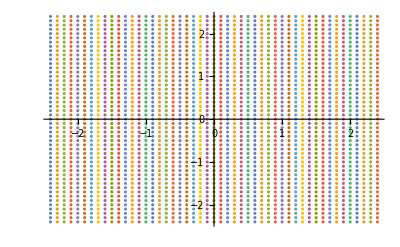

```mathematica
p1=ListPlot[lat]
```

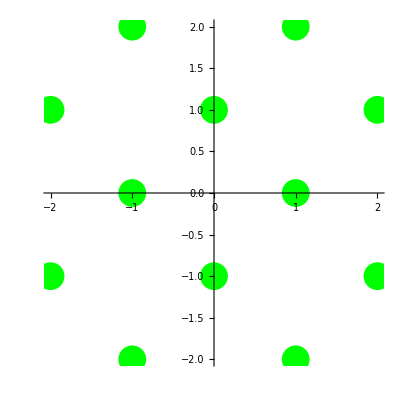

```mathematica
p2A=ListPlot[recA,PlotStyle->{PointSize->0.05,Green},AspectRatio->1]
```

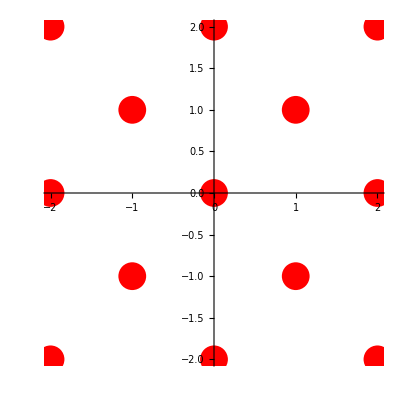

```mathematica
p2B=ListPlot[recB,PlotStyle->{PointSize->0.05,Red},AspectRatio->1]
```

```mathematica
pospos={}; (* coordinates of the probing points nearest to the nodes *)
```

```mathematica
Map[pospos={};AppendTo[pospos,lat[[#[[1]], #[[2]]]]]&, pos];
```

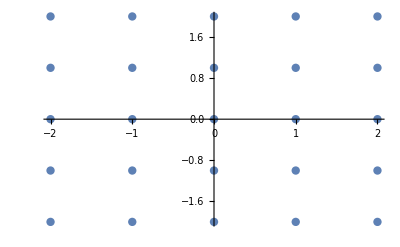

```mathematica
p4=ListPlot[pospos,PlotStyle->{PointSize->0.015}]
```

```mathematica
neighpospos={};
```

```mathematica
Map[neighpospos={};AppendTo[neighpospos,lat[[#[[1]], #[[2]]]]]&, Flatten[neighpos,1]];
```

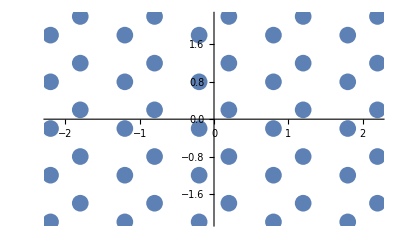

```mathematica
p5=ListPlot[neighpospos,PlotStyle->{PointSize->0.03}]
```

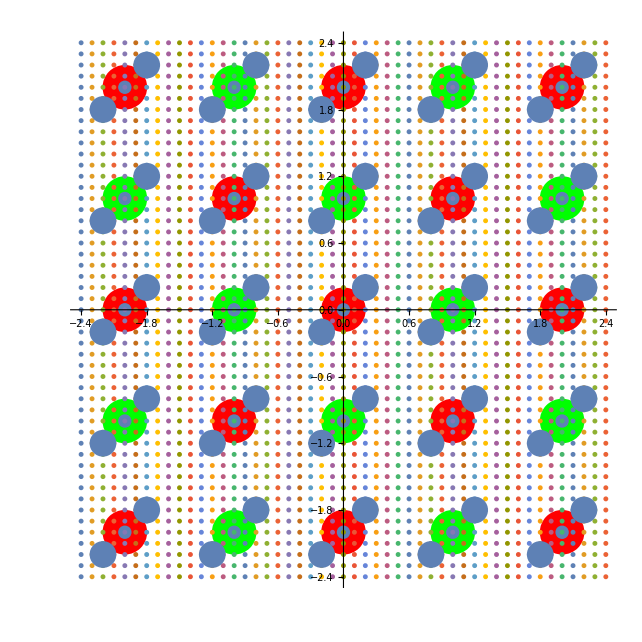

```mathematica
Show[ p2A,p2B,p4,p1,p5,PlotRange->All]
```

```mathematica
w[r_,ri_,σw_,β_]:=β*Exp[-Norm[N[r]-N[ri]]^2/2/σw^2];
```

```mathematica
Needs["wavefunction`"]
```

```mathematica
β=wannierNormalisationFactor[σw,δx,δy,lat]
```

Thread::tdlen: Objects of unequal length in {{-2.4,-2.4},{-2.4,-2.3},{-2.4,-2.2},{-2.4,-2.1},{-2.4,-2.},{-2.4,-1.9},{-2.4,-1.8},«35»,{-2.4,1.8},{-2.4,1.9},{-2.4,2.},{-2.4,2.1},{-2.4,2.2},{-2.4,2.3},{-2.4,2.4}}+«1» cannot be combined.

Thread::tdlen: Objects of unequal length in {{-2.3,-2.4},{-2.3,-2.3},{-2.3,-2.2},{-2.3,-2.1},{-2.3,-2.},{-2.3,-1.9},{-2.3,-1.8},«35»,{-2.3,1.8},{-2.3,1.9},{-2.3,2.},{-2.3,2.1},{-2.3,2.2},{-2.3,2.3},{-2.3,2.4}}+«1» cannot be combined.

Thread::tdlen: Objects of unequal length in {{-2.2,-2.4},{-2.2,-2.3},{-2.2,-2.2},{-2.2,-2.1},«41»,{-2.2,2.1},{-2.2,2.2},{-2.2,2.3},{-2.2,2.4}}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

10./(√(ⅇ^(-41.6233 Norm[1]^2)+ⅇ^(-41.6233 1)+45+ⅇ^1+ⅇ^(-41.6233 1^2)))
 |  |  |  |

```mathematica
Plot3D[wannier[{x,y},{0,0},σw,β],{x,-2σw,2σw},{y,-2σw,2σw}]
```

Thread::tdlen: Objects of unequal length in {0.,0.}+{{-2.4,-2.4},{-2.4,-2.3},{-2.4,-2.2},{-2.4,-2.1},{-2.4,-2.},{-2.4,-1.9},{-2.4,-1.8},«36»,{-2.4,1.9},{-2.4,2.},{-2.4,2.1},{-2.4,2.2},{-2.4,2.3},{-2.4,2.4}} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.,0.}+{{-2.3,-2.4},{-2.3,-2.3},{-2.3,-2.2},{-2.3,-2.1},{-2.3,-2.},{-2.3,-1.9},{-2.3,-1.8},«36»,{-2.3,1.9},{-2.3,2.},{-2.3,2.1},{-2.3,2.2},{-2.3,2.3},{-2.3,2.4}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

-Graphics3D-

```mathematica
blochSphereAnglesHarper[{3.,2.},1.,2.]
```

{0.189072,0.272934}

```mathematica
wavef=waveFunctionHarper[lat,ax,ay,J,J1,rec,RTF,k0,σw,β];
```

Part::partd: Part specification 1.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification 1.⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ListPointPlot3D[Table[{Abs@wavef[[i]], lat[[i,1]], lat[[i,2]]},{i,Length[lat]}], AspectRatio->1,ColorFunction->"Rainbow"]
```

$Aborted

```mathematica
MapIndexed[f,lat,{2}]
```

{{f[{-2.,-2.},{1,1}],f[{-2.,-1.5},{1,2}],f[{-2.,-1.},{1,3}],f[{-2.,-0.5},{1,4}],f[{-2.,0.},{1,5}],f[{-2.,0.5},{1,6}],f[{-2.,1.},{1,7}],f[{-2.,1.5},{1,8}],f[{-2.,2.},{1,9}]},{f[{-1.5,-2.},{2,1}],f[{-1.5,-1.5},{2,2}],f[{-1.5,-1.},{2,3}],f[{-1.5,-0.5},{2,4}],f[{-1.5,0.},{2,5}],f[{-1.5,0.5},{2,6}],f[{-1.5,1.},{2,7}],f[{-1.5,1.5},{2,8}],f[{-1.5,2.},{2,9}]},{f[{-1.,-2.},{3,1}],f[{-1.,-1.5},{3,2}],f[{-1.,-1.},{3,3}],f[{-1.,-0.5},{3,4}],f[{-1.,0.},{3,5}],f[{-1.,0.5},{3,6}],f[{-1.,1.},{3,7}],f[{-1.,1.5},{3,8}],f[{-1.,2.},{3,9}]},{f[{-0.5,-2.},{4,1}],f[{-0.5,-1.5},{4,2}],f[{-0.5,-1.},{4,3}],f[{-0.5,-0.5},{4,4}],f[{-0.5,0.},{4,5}],f[{-0.5,0.5},{4,6}],f[{-0.5,1.},{4,7}],f[{-0.5,1.5},{4,8}],f[{-0.5,2.},{4,9}]},{f[{0.,-2.},{5,1}],f[{0.,-1.5},{5,2}],f[{0.,-1.},{5,3}],f[{0.,-0.5},{5,4}],f[{0.,0.},{5,5}],f[{0.,0.5},{5,6}],f[{0.,1.},{5,7}],f[{0.,1.5},{5,8}],f[{0.,2.},{5,9}]},{f[{0.5,-2.},{6,1}],f[{0.5,-1.5},{6,2}],f[{0.5,-1.},{6,3}],f[{0.5,-0.5},{6,4}],f[{0.5,0.},{6,5}],f[{0.5,0.5},{6,6}],f[{0.5,1.},{6,7}],f[{0.5,1.5},{6,8}],f[{0.5,2.},{6,9}]},{f[{1.,-2.},{7,1}],f[{1.,-1.5},{7,2}],f[{1.,-1.},{7,3}],f[{1.,-0.5},{7,4}],f[{1.,0.},{7,5}],f[{1.,0.5},{7,6}],f[{1.,1.},{7,7}],f[{1.,1.5},{7,8}],f[{1.,2.},{7,9}]},{f[{1.5,-2.},{8,1}],f[{1.5,-1.5},{8,2}],f[{1.5,-1.},{8,3}],f[{1.5,-0.5},{8,4}],f[{1.5,0.},{8,5}],f[{1.5,0.5},{8,6}],f[{1.5,1.},{8,7}],f[{1.5,1.5},{8,8}],f[{1.5,2.},{8,9}]},{f[{2.,-2.},{9,1}],f[{2.,-1.5},{9,2}],f[{2.,-1.},{9,3}],f[{2.,-0.5},{9,4}],f[{2.,0.},{9,5}],f[{2.,0.5},{9,6}],f[{2.,1.},{9,7}],f[{2.,1.5},{9,8}],f[{2.,2.},{9,9}]}}